Логаш Лаб6 Вар7

Интерполирование функций многих переменных: 
1. Выбираем ньютоновскую систему точек и систему одночленов степени не выше m и  n от переменных

10

{0,1,2,3}

{{0,0},{0,1},{0,2},{0,3},{1,0},{1,1},{1,2},{2,0},{2,1},{3,0}}

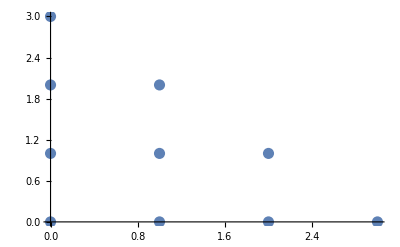

{1,y,y^2,y^3,x,x y,x y^2,x^2,x^2 y,x^3}

```mathematica
n=2;m=3;μ=((n+m)!)/(n!m!)
SS=Table[Subscript[S, i]=i,{i,0,m}]
t={};i=1; Do[If[j+k<m+1,{t=Join[t,{{Subscript[S, j],Subscript[S, k]}}],Subscript[ϕ, i][x_,y_]=x^Subscript[S, j] y^Subscript[S, k],i=i+1}],{j,0,m},{k,0,m}]
t
ListPlot[t,PlotStyle->PointSize[0.02]]
Table[Subscript[ϕ, i][x,y],{i,1,μ}]
```

2. Формируем матрицу Вандермонда и проверяем, что ее определитель для выбранных узлов интерполирования отличен от нуля

```mathematica
V=Table[Subscript[ϕ, j][t[[i,1]],t[[i,2]]],{i,1,μ},{j,1,μ}];
Det[V]≠ 0
```

True

3. Строим интерполяционный многочлен для произвольной функции f

```mathematica
eqv:=Table[∑_(i=1)^μ (Subscript[b, i]*Subscript[ϕ, i][t[[k,1]],t[[k,2]]])==f[t[[k,1]],t[[k,2]]],{k,1,μ}]
koef:=Solve[eqv,{}]//Flatten
P[x_,y_]:=∑_(i=1)^μ (Subscript[b, i]*Subscript[ϕ, i][x,y])/.koef
```

4. Получаем интерполяционный многочлен для заданной функции f

```mathematica
f[x_,y_]=2^x Sin[y];
P[x,y]//N
```

1.20751 y+0.807558 x y+0.420735 x^2 y-0.355643 y^2-0.386822 x y^2-0.0103932 y^3

5.Проверяем выполнение интерполяционных условий

```mathematica
Table[P[t[[i,1]],t[[i,2]]]-f[t[[i,1]],t[[i,2]]],{i,1,μ}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0}

6. Изображаем узлы, исходную функцию и полученный интерполяционный многочлен в одной системе координат

```mathematica
mm=Min[SS];MM=Max[SS];
g1=Plot3D[f[x,y],{x,mm,MM},{y,mm,MM}];
g2=Plot3D[P[x,y],{x,mm,MM},{y,mm,MM}];
Tbl=Table[Point[{t[[i,1]],t[[i,2]],f[t[[i,1]],t[[i,2]]]}],{i,1,μ}];
g3=Graphics3D[{AbsolutePointSize[8],Tbl}];
Show[g1,g2,g3]
```

-Graphics3D-

7. Убеждаемся в инвариантности интерполяционной формулы для одночленов степени не выше m

```mathematica
Table[{f[x_,y_]=Subscript[ϕ, i][x,y],P[x,y]==Subscript[ϕ, i][x,y]},{i,1,μ}]
```

{{1,True},{y,True},{y^2,True},{y^3,True},{x,True},{x y,True},{x y^2,True},{x^2,True},{x^2 y,True},{x^3,True}}